## A reanalysis of the SH0ES data for H_0. Reanalysis of Individual Cepheid m_H^W slope data. Homogeneity of the Cepheid modeling parameter b_W.

## Setting the directory

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["ErrorBarPlots`"];
Needs["ErrorBarLogPlots`"]
Off[General::"obspkg",General::luc,NIntegrate::"inumr",NIntegrate::ncvb,CompiledFunction::cflist,ListInterpolation::inhr,FindMinimum::lstol];
```

## Matrix of Measurements Y - Data - Error Matrix C

```mathematica
ClearAll["Global`*"] 
Clear["Global`*"]
```

```mathematica
ydata=Import[".\\data\\ally_shoes_ceph_topantheonwt6.0_112221.fits","RawData"];
```

```mathematica
dataperiod=Import[".\\data\\logp.txt","Table"];
```

```mathematica
galrank=Import[".\\data\\galrank.txt","Table"];
```

```mathematica
cdata=Import[".\\data\\allc_shoes_ceph_topantheonwt6.0_112221.fits","RawData"];
```

## Fitting individual slopes b_W of the Cepheid P-L relations (ignored non-diagonal terms)- Figure C1

```mathematica
l=0;
```

```mathematica
k=1;
```

```mathematica
g=1;
```

```mathematica
taballnocov={};
tabcsplotnocov={};
tabfigcsnocov={};
tabcsnocov={};
tabfigcsnocovinset={};
Do[
name=galrank[[g,4]];(*name of galaxy *)
galP[dataperiod_]:=Table[dataperiod[[i,1]]+1,{i,k+l,n}];(*period data *)
PER=galP[dataperiod];
galMW[ydata_]:=Table[If[n>2648, ydata[[1,i]]+18.47-3.286*(PER[[i-l]]-1),If[2150<n<2594, ydata[[1,i]]+29.397-3.286*(PER[[i-l]]-1),ydata[[1,i]]-3.286*(PER[[i-l]]-1)]],{i,k+l,n}];
Y=galMW[ydata];(*Subscript[m, H]^W data *)
qpar[q1_,q2_]:={q1,q2};
L=Table[{1,galP[dataperiod][[i]]},{i,Length[PER]}];(*matrix A, see Eq.23 *)
trL=Transpose[L];
galc=Take[cdata[[1]],{k+l,n},{k+l,n}];
dgalc=Diagonal[galc];
Call=DiagonalMatrix[dgalc];(*matrix C, see Eqs. 25, 26 *)
tablecs[PER_,Y_,Call_]:=Table[{PER[[i]],Y[[i]],Sqrt[Call[[i,i]]]},{i,1,Length[PER]}];
CS=tablecs[PER,Y,Call];
InvCall=Inverse[Call];
sigma=Inverse[trL.InvCall.L];(* matrix Σ, see Eq.26 *)
qbf=sigma.(trL.InvCall.Y);(* best fit values *)

vec[q1_,q2_]:=Y-L.qpar[q1,q2];
chi2[q1_,q2_]:=vec[q1,q2].InvCall.vec[q1,q2 ];
chi2min=FindMinimum[chi2[q1,q2],{q1,qbf[[1]]},{q2,qbf[[2]]}];
Na=n-l;
CSplot=If[n>2648,ErrorListPlot[CS,Frame->True,Axes->None,BaseStyle->FontSize->20,PlotRange->{{0.6,2.},{8,15}},FrameLabel->{"log Period (days)","m_H^W  (mag)"},PlotStyle->{PointSize->Medium,Red},FrameStyle->Directive[Black,Thick],ImageSize->Large], If[2593<n<2649,ErrorListPlot[CS,Frame->True,Axes->None,BaseStyle->FontSize->20,PlotRange->{{0.6,2.},{14,21}},FrameLabel->{"log Period (days)","m_H^W  (mag)"},PlotStyle->{PointSize->Medium,Red},FrameStyle->Directive[Black,Thick],ImageSize->Large], ErrorListPlot[CS,Frame->True,Axes->None,BaseStyle->FontSize->20,PlotRange->{{0.6,2.2},{20,29}},FrameLabel->{"log Period (days)","m_H^W  (mag)"},PlotStyle->{PointSize->Medium,Red},FrameStyle->Directive[Black,Thick],ImageSize->Large]]];
figcsinset=If[ 381<n<428,Show[CSplot,Graphics[{Inset[name ,{0.9,21.1},BaseStyle->{Italic,Black,FontFamily->"Times",8}]}],Graphics[{Inset[Round[chi2min[[2,1,2]],0.01]+Round[chi2min[[2,2,2]],0.01]"log P",{1.4,26.3},BaseStyle->{Italic,Bold,Purple,FontFamily->"Times",8}]}],Graphics[{Inset[28.7-3.27"log P",{1.4,27.5},BaseStyle->{Italic,Bold,Darker[Green],FontFamily->"Times",8}]}],Graphics[{Inset[Na " Cepheids",{0.9,21.9},BaseStyle->{Italic,Black,FontFamily->"Times",8}]}],FrameLabel->{"log Period (days)","m_H^W  (mag)"},PlotRange->{{0.6,2.2},{20,29}},Epilog->{{Dashed,Purple,Line[{{0,chi2min[[2,1,2]]},{3,chi2min[[2,1,2]]+3*chi2min[[2,2,2]]}}]},{Dashed,Darker[Green],Line[{{0,28.7},{2.2,21.5}}]}},LabelStyle->{Bold,FontFamily->"Times",8},Axes->None,FrameStyle->Directive[Black],Frame->True,ImageSize->Large],If[ 1309<n<1319,Show[CSplot,Graphics[{Inset[name ,{0.9,21.1},BaseStyle->{Italic,Black,FontFamily->"Times",8}]}],Graphics[{Inset[Round[chi2min[[2,1,2]],0.01]+Round[chi2min[[2,2,2]],0.01]"log P",{1.4,26.3},BaseStyle->{Italic,Bold,Purple,FontFamily->"Times",8}]}],Graphics[{Inset[28.2-3.27"log P",{1.4,27.5},BaseStyle->{Italic,Bold,Darker[Green],FontFamily->"Times",8}]}],Graphics[{Inset[Na " Cepheids",{0.9,21.9},BaseStyle->{Italic,Black,FontFamily->"Times",8}]}],FrameLabel->{"log Period (days)","m_H^W  (mag)"},PlotRange->{{0.6,2.2},{20,29}},Epilog->{{Dashed,Purple,Line[{{0,chi2min[[2,1,2]]},{3,chi2min[[2,1,2]]+3*chi2min[[2,2,2]]}}]},{Dashed,Darker[Green],Line[{{0,28.2},{2.2,21}}]}},LabelStyle->{Bold,FontFamily->"Times",8},Axes->None,FrameStyle->Directive[Black],Frame->True,ImageSize->Large]]];
figcs=If[ 381<n<428,Show[CSplot,Graphics[{Inset[name ,{0.9,21.1},BaseStyle->{Italic,Black,FontFamily->"Times",18}]}],Graphics[{Inset[Round[chi2min[[2,1,2]],0.01]+Round[chi2min[[2,2,2]],0.01]"log P",{1.4,26.3},BaseStyle->{Italic,Bold,Purple,FontFamily->"Times",16}]}],Graphics[{Inset[28.7-3.27"log P",{1.4,27.5},BaseStyle->{Italic,Bold,Darker[Green],FontFamily->"Times",8}]}],Graphics[{Inset[Na " Cepheids",{0.9,21.9},BaseStyle->{Italic,Black,FontFamily->"Times",8}]}],FrameLabel->{"log Period (days)","m_H^W  (mag)"},PlotRange->{{0.6,2.2},{20,29}},Epilog->{{Dashed,Purple,Line[{{0,chi2min[[2,1,2]]},{3,chi2min[[2,1,2]]+3*chi2min[[2,2,2]]}}]},{Dashed,Darker[Green],Line[{{0,28.7},{2.2,21.5}}]}},LabelStyle->{Bold,FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black],Frame->True,ImageSize->Large],If[ 1309<n<1319,Show[CSplot,Graphics[{Inset[name ,{0.9,21.1},BaseStyle->{Italic,Black,FontFamily->"Times",18}]}],Graphics[{Inset[Round[chi2min[[2,1,2]],0.01]+Round[chi2min[[2,2,2]],0.01]"log P",{1.4,26.3},BaseStyle->{Italic,Bold,Purple,FontFamily->"Times",16}]}],Graphics[{Inset[28.2-3.27"log P",{1.4,27.5},BaseStyle->{Italic,Bold,Darker[Green],FontFamily->"Times",8}]}],Graphics[{Inset[Na " Cepheids",{0.9,21.9},BaseStyle->{Italic,Black,FontFamily->"Times",8}]}],FrameLabel->{"log Period (days)","m_H^W  (mag)"},PlotRange->{{0.6,2.2},{20,29}},Epilog->{{Dashed,Purple,Line[{{0,chi2min[[2,1,2]]},{3,chi2min[[2,1,2]]+3*chi2min[[2,2,2]]}}]},{Dashed,Darker[Green],Line[{{0,28.2},{2.2,21}}]}},LabelStyle->{Bold,FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black],Frame->True,ImageSize->Large],If[n>2648,Show[CSplot,Graphics[{Inset[name ,{1.,9.},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[Round[chi2min[[2,1,2]],0.01]+Round[chi2min[[2,2,2]],0.01]"log P",{1.6,13.5},BaseStyle->{Italic,Bold,Purple,FontFamily->"Times",16}]}],Graphics[{Inset[Na " Cepheids",{1.,9.5},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],FrameLabel->{"log Period (days)","m_H^W  (mag)"},PlotRange->{{0.6,2.},{8,15}},Epilog->{{Dashed,Purple,Line[{{0,chi2min[[2,1,2]]},{3,chi2min[[2,1,2]]+3*chi2min[[2,2,2]]}}]}},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,ImageSize->Large],If[2150<n<2594,Show[CSplot,Graphics[{Inset[name ,{0.9,21.3},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[Round[chi2min[[2,1,2]],0.01]+Round[chi2min[[2,2,2]],0.01]"log P",{1.4,28.},BaseStyle->{Italic,Bold,Purple,FontFamily->"Times",16}]}],Graphics[{Inset[Na " Cepheids",{0.9,21.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],FrameLabel->{"log Period (days)","m_H^W  (mag)"},PlotRange->{{0.6,2.},{20,29}},Epilog->{{Dashed,Purple,Line[{{0,chi2min[[2,1,2]]},{3,chi2min[[2,1,2]]+3*chi2min[[2,2,2]]}}]}},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,ImageSize->Large],If[2593<n<2649,Show[CSplot,Graphics[{Inset[name ,{0.9,15.},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[Round[chi2min[[2,1,2]],0.01]+Round[chi2min[[2,2,2]],0.01]"log P",{1.4,15},BaseStyle->{Italic,Bold,Purple,FontFamily->"Times",16}]}],Graphics[{Inset[Na " Cepheids",{0.9,15.5},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],FrameLabel->{"log Period (days)","m_H^W  (mag)"},PlotRange->{{0.6,2.},{14,21}},Epilog->{{Dashed,Purple,Line[{{0,chi2min[[2,1,2]]},{3,chi2min[[2,1,2]]+3*chi2min[[2,2,2]]}}]}},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,ImageSize->Large],If[n<260,Show[CSplot,Graphics[{Inset[name ,{0.9,21.},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[Round[chi2min[[2,1,2]],0.01]+Round[chi2min[[2,2,2]],0.01]"log P",{1.4,28.},BaseStyle->{Italic,Bold,Purple,FontFamily->"Times",16}]}],Graphics[{Inset[Na " Cepheids",{0.9,21.5},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],FrameLabel->{"log Period (days)","m_H^W  (mag)"},PlotRange->{{0.6,2.2},{20,29}},Epilog->{{Dashed,Purple,Line[{{0,chi2min[[2,1,2]]},{3,chi2min[[2,1,2]]+3*chi2min[[2,2,2]]}}]}},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,ImageSize->Large],Show[CSplot,Graphics[{Inset[name ,{0.9,21.3},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[Round[chi2min[[2,1,2]],0.01]+Round[chi2min[[2,2,2]],0.01]"log P",{1.4,21.3},BaseStyle->{Italic,Bold,Purple,FontFamily->"Times",16}]}],Graphics[{Inset[Na " Cepheids",{0.9,21.8},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],FrameLabel->{"log Period (days)","m_H^W  (mag)"},PlotRange->{{0.6,2.2},{20,29}},Epilog->{{Dashed,Purple,Line[{{0,chi2min[[2,1,2]]},{3,chi2min[[2,1,2]]+3*chi2min[[2,2,2]]}}]}},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black,Thick],Frame->True,ImageSize->Large]]]]]]];
AppendTo[tabcsnocov,{l+k,n,n-l,CS}];
AppendTo[tabcsplotnocov,{name,CSplot}];
AppendTo[tabfigcsnocovinset,{name,figcsinset}];
AppendTo[tabfigcsnocov,{name,figcs}];
l=n;
g=g+1;
AppendTo[taballnocov,{chi2min[[1]],chi2min[[2,1,2]],Sqrt[sigma[[1,1]]],chi2min[[2,2,2]],Sqrt[sigma[[2,2]]]}],
{n,{259,274,302,320,328,381,427,500,610,787,860,882,898,925,973,1046,1147,1201,1253,1280,1309,1318,1358,1388,1399,1492,1657,1908,1928,1969,1983,2004,2035,2068,2084,2117,2150,2593,2648,3130}}]
```

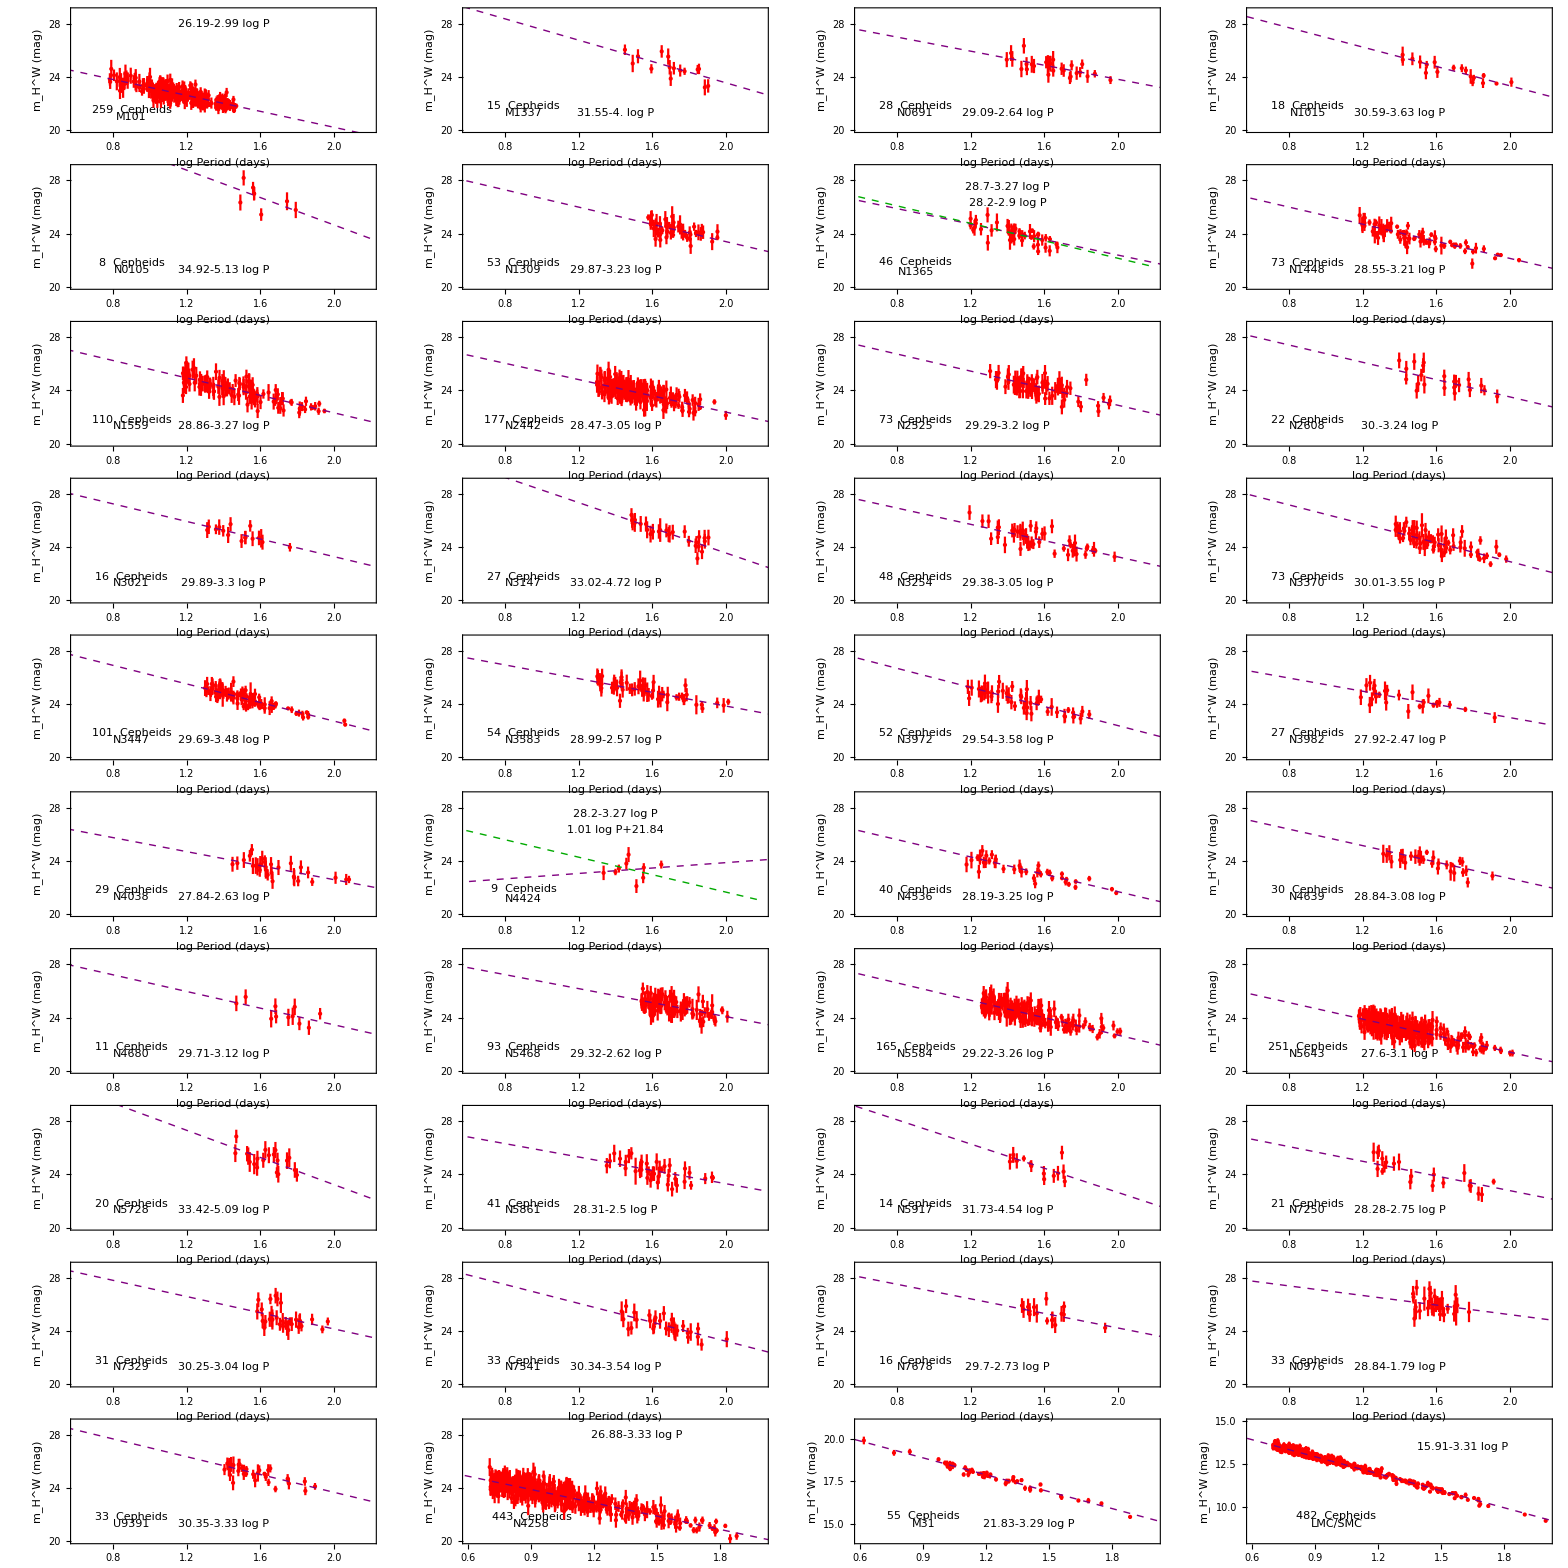

```mathematica
figballnocov=GraphicsGrid[{{tabfigcsnocov[[1,2]],tabfigcsnocov[[2,2]],tabfigcsnocov[[3,2]],tabfigcsnocov[[4,2]]},{tabfigcsnocov[[5,2]],tabfigcsnocov[[6,2]],tabfigcsnocov[[7,2]],tabfigcsnocov[[8,2]]},{tabfigcsnocov[[9,2]],tabfigcsnocov[[10,2]],tabfigcsnocov[[11,2]],tabfigcsnocov[[12,2]]},{tabfigcsnocov[[13,2]],tabfigcsnocov[[14,2]],tabfigcsnocov[[15,2]],tabfigcsnocov[[16,2]]},{tabfigcsnocov[[17,2]],tabfigcsnocov[[18,2]],tabfigcsnocov[[19,2]],tabfigcsnocov[[20,2]]},{tabfigcsnocov[[21,2]],tabfigcsnocov[[22,2]],tabfigcsnocov[[23,2]],tabfigcsnocov[[24,2]]},{tabfigcsnocov[[25,2]],tabfigcsnocov[[26,2]],tabfigcsnocov[[27,2]],tabfigcsnocov[[28,2]]},{tabfigcsnocov[[29,2]],tabfigcsnocov[[30,2]],tabfigcsnocov[[31,2]],tabfigcsnocov[[32,2]]},{tabfigcsnocov[[33,2]],tabfigcsnocov[[34,2]],tabfigcsnocov[[35,2]],tabfigcsnocov[[36,2]]},{tabfigcsnocov[[37,2]],tabfigcsnocov[[38,2]],tabfigcsnocov[[39,2]],tabfigcsnocov[[40,2]]}},Spacings->0]
```

```mathematica
Export[NotebookDirectory[]<>"figballnocov.pdf",figballnocov,ImageResolution->1000];
```

## Independently fitted slopes b_W of the Cepheid P-L relations (ignored non-diagonal terms) - Figure 1

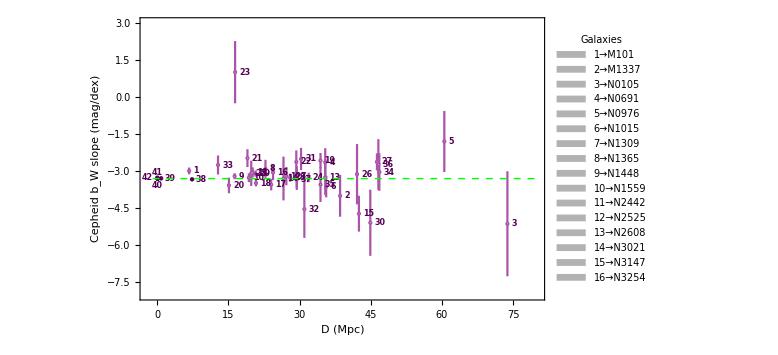

```mathematica
slopeernocov[galrank_,taballnocov_]:=Table[{galrank[[i,5]],taballnocov[[i,4]],taballnocov[[i,5]]},{i,1,40}]
slernocov=Join[slopeernocov[galrank,taballnocov],{{0.06,-3.310934547,0.01663741638281},{0,-3.26192,0.051433}}];
plslernocov=ErrorListPlot[slernocov,Frame->True,Axes->None,BaseStyle->FontSize->20,PlotRange->{{-1,80},{-8,2.5}},FrameLabel->{"D (Mpc)","Cepheid b_W slope (mag/dex)"},PlotStyle->{PointSize->Medium,Lighter[Purple]},Epilog->{Dashed,Green,Line[{{-1,-3.3},{80,-3.3}}]},ImageSize->Large];
legendnocov=SwatchLegend[{Purple,Purple,Purple,Purple,Purple,Purple,Purple,Purple,Purple,Purple,Purple,Purple,Purple,Purple,Purple,Purple,Purple,Purple,Purple,Purple,Purple,Purple,Purple,Purple,Purple,Purple,Purple,Purple,Purple,Purple,Purple,Purple,Purple,Purple,Purple,Purple,Purple,Purple,Purple,Purple,Purple,Purple},{galrank[[1,1]] ->galrank[[1,4]]  ,galrank[[2,1]] ->galrank[[2,4]] ,galrank[[5,1]] ->galrank[[5,4]] ,galrank[[3,1]] ->galrank[[3,4]] ,galrank[[36,1]] ->galrank[[36,4]],galrank[[4,1]] ->galrank[[4,4]] ,galrank[[6,1]] ->galrank[[6,4]] ,galrank[[7,1]] ->galrank[[7,4]] ,galrank[[8,1]] ->galrank[[8,4]] ,galrank[[9,1]] ->galrank[[9,4]],galrank[[10,1]] ->galrank[[10,4]],galrank[[11,1]] ->galrank[[11,4]],galrank[[12,1]] ->galrank[[12,4]],galrank[[13,1]] ->galrank[[13,4]],galrank[[14,1]] ->galrank[[14,4]],galrank[[15,1]] ->galrank[[15,4]],galrank[[16,1]] ->galrank[[16,4]]  ,galrank[[17,1]] ->galrank[[17,4]] ,galrank[[18,1]] ->galrank[[18,4]] ,galrank[[19,1]] ->galrank[[19,4]] ,galrank[[20,1]] ->galrank[[20,4]] ,galrank[[21,1]] ->galrank[[21,4]] ,galrank[[22,1]] ->galrank[[22,4]] ,galrank[[23,1]] ->galrank[[23,4]] ,galrank[[24,1]] ->galrank[[24,4]],galrank[[25,1]] ->galrank[[25,4]],galrank[[26,1]] ->galrank[[26,4]],galrank[[27,1]] ->galrank[[27,4]],galrank[[28,1]] ->galrank[[28,4]],galrank[[29,1]] ->galrank[[29,4]],galrank[[30,1]] ->galrank[[30,4]],galrank[[31,1]] ->galrank[[31,4]] ,galrank[[32,1]] ->galrank[[32,4]] ,galrank[[33,1]] ->galrank[[33,4]] ,galrank[[34,1]] ->galrank[[34,4]],galrank[[35,1]] ->galrank[[35,4]],galrank[[37,1]] ->galrank[[37,4]],38->N4258,39->M31,40->LMC,41->SMC,42->MW},LegendLayout->{"Column",2},LabelStyle->{Bold,Darker[Purple],FontSize->9},LegendMarkers->Graphics[{Black,Opacity[0.3],Disk[]}],LegendLabel->"Galaxies",LegendMarkerSize->6,LegendFunction->(Framed[#,RoundingRadius->3,FrameStyle->White]&),LegendMargins->0.1];
plslerlabelnocov=ListPlot[Table[Labeled[{galrank[[i,5]],taballnocov[[i,4]]},galrank[[i,1]],Right],{i,1,37}],Axes->False, Frame->True,BaseStyle->FontSize->8,LabelStyle->Directive[Bold,FontFamily->"Helvetica",8,Darker[Purple]],PlotRange->{{-1,80},{-7,-0.3}},PlotStyle->{PointSize[0.00001],White},PlotLegends->legendnocov,ImageSize->Large];
lab2nocov=ListPlot[{Labeled[{0,-3.26192},"  42" ,Left],Labeled[{0.05,taballnocov[[40,4]]},"  40" ,Bottom],Labeled[{0.06,taballnocov[[40,4]]},"  41" ,Top],Labeled[{7.3,taballnocov[[38,4]]},"  38",Right],Labeled[{0.76,taballnocov[[39,4]]},"  39" ,Right]},
Frame->True,Axes->None,LabelStyle->Directive[Bold,FontFamily->"Helvetica",8,Darker[Purple],Spacings->4],BaseStyle->FontSize->20,PlotRange->{{-2,40},{-5,1}},PlotStyle->{PointSize->Small,Darker[Purple]}];
figb10dnocov=Show[plslernocov,plslerlabelnocov,lab2nocov,FrameStyle->Directive[Black,Thick,FontFamily->"Times",20],PlotRange->{{-2,80},{-8,3.}},Frame->True,ImageSize->Large]
```

```mathematica
Export[NotebookDirectory[]<>"figb10dnocov.pdf",figb10dnocov,ImageResolution->1000];
```

## Independently fitted slopes b_W of the Cepheid P-L relations (ignored non-diagonal terms) - Purple points of Figure C3

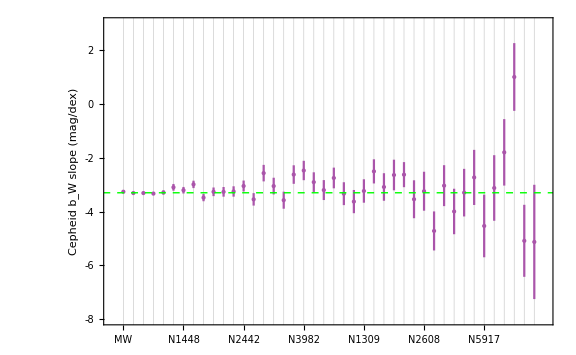

```mathematica
slopeer2nocov[galrank_,taballnocov_]:=Table[{galrank[[i,3]],taballnocov[[i,4]],taballnocov[[i,5]]},{i,1,40}]
sler2nocov=Join[slopeer2nocov[galrank,taballnocov],{{3,-3.310934547105,0.016637},{1,-3.26192,0.051433}}];
plsler2nocov=ErrorListPlot[sler2nocov,Frame->True,Axes->None,BaseStyle->FontSize->20,PlotRange->{{-1,44},{-8,2.5}},GridLines->{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42},None},FrameLabel->{"","Cepheid b_W slope (mag/dex)"},PlotStyle->{PointSize->Medium,Lighter[Purple]},Epilog->{Dashed,Green,Line[{{-1,-3.3},{80,-3.3}}]},ImageSize->Large];
figb10nocov=Show[plsler2nocov,FrameStyle->Directive[Black,Thick],FrameTicks->{{{-8,-6,-4,-2,0,2},None},{{{1,Rotate["MW",90 Degree]},{2,Rotate["LMC",90 Degree]},{3,Rotate["SMC",90 Degree]},{4,Rotate["N4258",90 Degree]},{5,Rotate["M31",90 Degree]},{6,Rotate["N5643",90 Degree]},{7,Rotate["N1448",90 Degree]},{8,Rotate["M101",90 Degree]},{9,Rotate["N3447",90 Degree]},{10,Rotate["N5584",90 Degree]},{11,Rotate["N1559",90 Degree]},{12,Rotate["N4536",90 Degree]},{13,Rotate["N2442",90 Degree]},{14,Rotate["N3370",90 Degree]},{15,Rotate["N3583",90 Degree]},{16,Rotate["N3254",90 Degree]},{17,Rotate["N3972",90 Degree]},{18,Rotate["N5468",90 Degree]},{19,Rotate["N3982",90 Degree]},{20,Rotate["N1365",90 Degree]},{21,Rotate["N2525",90 Degree]},{22,Rotate["N7250",90 Degree]},{23,Rotate["U9391",90 Degree]},{24,Rotate["N1015",90 Degree]},{25,Rotate["N1309",90 Degree]},{26,Rotate["N5861",90 Degree]},{27,Rotate["N4639",90 Degree]},{28,Rotate["N0691",90 Degree]},{29,Rotate["N4038",90 Degree]},{30,Rotate["N7541",90 Degree]},{31,Rotate["N2608",90 Degree]},{32,Rotate["N3147",90 Degree]},{33,Rotate["N7329",90 Degree]},{34,Rotate["M1337",90 Degree]},{35,Rotate["N3021",90 Degree]},{36,Rotate["N7678",90 Degree]},{37,Rotate["N5917",90 Degree]},{38,Rotate["N4680",90 Degree]},{39,Rotate["N0976",90 Degree]},{40,Rotate["N4424",90 Degree]},{41,Rotate["N5728",90 Degree]},{42,Rotate["N0105",90 Degree]}},None}},PlotRange->{{-0.1,43},{-8,3.}},FrameTicksStyle->Directive[Thick,Black,FontFamily->"Helvetica",12], Frame->True,ImageSize->Large]
```

## Homogeneity of the Cepheid modeling parameter b_W - Binned Cepheid P-L slopes b_W for the high distance bin (D>Dc) and the low distance bin (D<Dc) - Figure 3

```mathematica
chi2nocov [z_?NumberQ]:=Sum[((slernocov[[i,2]]-z)/Sqrt[slernocov[[i,3]]^2+0.^2])^2,{i,1,42}];(* see Eq.30 (Subscript[σ, scat]=0) *)
chi2minnocov=FindMinimum[chi2nocov [z],{z,0}]
```

{63.4319,{z→-3.30088}}

```mathematica
chired=chi2minnocov[[1]]/41
```

1.54712

```mathematica
chi2nocov [z_?NumberQ]:=Sum[((slernocov[[i,2]]-z)/Sqrt[slernocov[[i,3]]^2+0.18^2])^2,{i,1,42}];(*  see Eq.30 (Subscript[σ, scat]=0.18)*)
chi2minnocov=FindMinimum[chi2nocov [z],{z,0}]
```

{44.5342,{z→-3.20318}}

```mathematica
chired=chi2minnocov[[1]]/41
```

1.0862

```mathematica
tabdssdnocov={};
tabbfwnocov ={};
tabbfwsnocov={};
tabbfwlnocov ={};
tabchired={};
Do[
slersnocov=Select[slernocov,#[[1]]<dspltnocov &];

slerlnocov=Select[slernocov,#[[1]]>dspltnocov &];

If[dspltnocov<10,chi2snocov [w_?NumberQ]:=Sum[((slersnocov[[i,2]]-w)/Sqrt[slersnocov[[i,3]]^2+0.04^2])^2,{i,1,Length[slersnocov]}],chi2snocov [w1_?NumberQ]:=Sum[((slersnocov[[i,2]]-w1)/Sqrt[slersnocov[[i,3]]^2+0.18^2])^2,{i,1,Length[slersnocov]}]];
chi2sminnocov=FindMinimum[chi2snocov [w],{w,-3.3}];
wminsnocov =chi2sminnocov [[2,1,2]];
chi2smincnocov =chi2sminnocov [[1]];
s11snocov =FindRoot[chi2snocov [w]==chi2sminnocov [[1]]+1,{w,chi2sminnocov [[2,1,2]]+0.5}][[1,2]]-chi2sminnocov [[2,1,2]];
If[dspltnocov>43,chi2lnocov [w_?NumberQ]:=Sum[((slerlnocov[[i,2]]-w)/Sqrt[slerlnocov[[i,3]]^2+0.04^2])^2,{i,1,Length[slerlnocov]}]  ,chi2lnocov [w_?NumberQ]:=Sum[((slerlnocov[[i,2]]-w)/Sqrt[slerlnocov[[i,3]]^2+0.18^2])^2,{i,1,Length[slerlnocov]}]];
chi2lminnocov =FindMinimum[chi2lnocov [w],{w,-3.1}];
wminlnocov =chi2lminnocov [[2,1,2]];
chi2lmincnocov =chi2lminnocov [[1]];
s11lnocov =FindRoot[chi2lnocov [w]==chi2lminnocov [[1]]+1,{w,chi2lminnocov [[2,1,2]]+0.5}][[1,2]]-chi2lminnocov [[2,1,2]];

sdistminnocov =Abs[(wminlnocov -wminsnocov)]/(s11lnocov ^2+s11snocov ^2)^0.5;
AppendTo[tabchired,{dspltnocov,chi2sminnocov[[1]]/ Length[slersnocov],chi2lminnocov [[1]]/Length[slerlnocov]}];
AppendTo[tabbfwnocov,{dspltnocov,wminsnocov ,wminlnocov }];
AppendTo[tabbfwsnocov ,{dspltnocov,wminsnocov ,s11snocov }];
AppendTo[tabbfwlnocov ,{dspltnocov,wminlnocov ,s11lnocov }];
AppendTo[tabdssdnocov ,{dspltnocov,sdistminnocov }],{dspltnocov,0.55,59.55,1}]
```

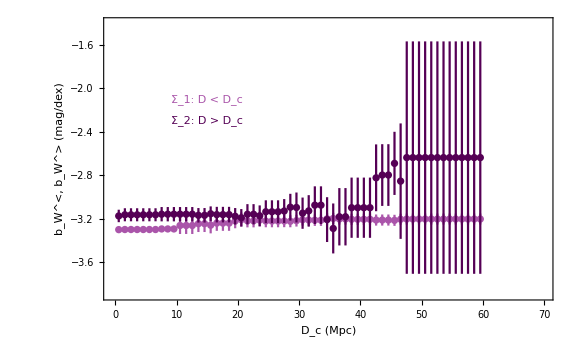

```mathematica
figwslinnocov=ErrorListPlot[{tabbfwsnocov,tabbfwlnocov},Frame->True,FrameLabel->{"D_c [Mpc]","b_W^<, b_W^> (mag/dex)"},BaseStyle->{Medium,GrayLevel[.3],FontFamily->"Times",8},LabelStyle->Directive[GrayLevel[.3],Small],PlotRange->{{-0.5,37},{-3.5,-3.}},PlotStyle->{Lighter[Purple],Darker[Purple]},FrameStyle -> Directive[GrayLevel[.3], Thick],ImageSize->250];
figbfsets=ErrorListPlot[{tabbfwsnocov,tabbfwlnocov},Frame->True,FrameLabel->{"D_c (Mpc)","b_W^<, b_W^>  (mag/dex)"},BaseStyle->{Large,FontFamily->"Times",20},LabelStyle->Directive[Black,Large],PlotRange->{{-0.5,70},{-3.9,-1.4}},PlotStyle->{Lighter[Purple],Darker[Purple]},ImageSize->Large, FrameStyle -> Directive[Black, Thick],Epilog->{{Lighter[Purple],Inset["Σ_1: D < D_c",{15,-2.1}]},{Darker[Purple],Inset["Σ_2: D > D_c",{15,-2.3}]}}]
Export[NotebookDirectory[]<>"figbfsets.pdf",figbfsets,ImageResolution->1000];
```

## σ-distance between the best fit high bin and low bin slopes b_W- Figure 5 (purple curve)

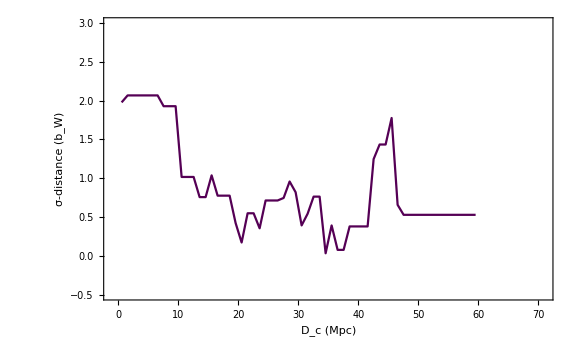

```mathematica
figwsdnocov=ListPlot[tabdssdnocov,Frame->True,Joined->True,FrameLabel->{"D_c (Mpc)","σ-distance (b_W)"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotRange->{{-1,71},{-0.5,3}},Axes->False,PlotStyle->{Darker[Purple]},ImageSize->Large, FrameStyle -> Directive[Black, Thick]]
```

## Independently fitted slopes bW of the Cepheid P-L relations from Fig. 10 of Riess 21 (data obtained using plot digitizer) - Green points of Figure C3

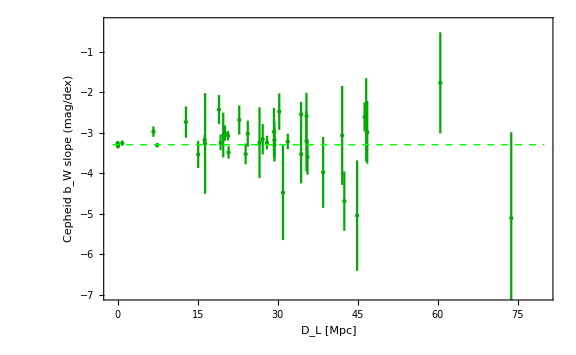

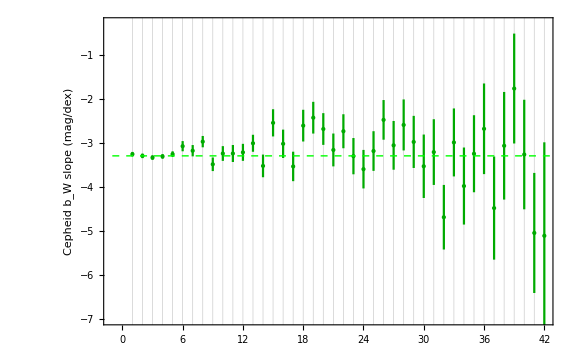

```mathematica
datablack=Import[".\\data\\galblack.txt","Table"];
yblack[datablack_]:=Table[datablack[[i,2]],{i,1,Length[datablack]}];
datablacker=Import[".\\data\\galblacker.txt","Table"];
yblacker[datablacker_]:=Table[datablacker[[i,2]],{i,1,Length[datablacker]}];
datadist=Import[".\\data\\dist.txt","Table"];
ydist[datadist_]:=Table[datadist[[i,2]],{i,1,Length[datadist]}];
ydist[datadist];
ydlblack[datadist_,datablack_,datablacker_]:=Table[{datadist[[i,2]],datablack[[i,2]],datablacker[[i,2]]-datablack[[i,2]]},{i,1,Length[datablack]}]
testblack=ydlblack[datadist,datablack,datablacker];
ydlblack2[datablack_,datablacker_]:=Table[{datablack[[i,1]],datablack[[i,2]],datablacker[[i,2]]-datablack[[i,2]]},{i,1,Length[datablack]}]
testblack2=ydlblack2[datablack,datablacker];
pllabel=ListPlot[Table[Labeled[{i,datablack[[i,2]]},i,Right],{i,1,42}],Axes->False, Frame->True,BaseStyle->FontSize->8,LabelStyle->Directive[Bold,FontFamily->"Helvetica",8,Darker[Purple]],PlotRange->{{-1,80},{-7,-0.3}},PlotStyle->{PointSize[0.00001],White},ImageSize->Large];
plblack=ErrorListPlot[testblack,Frame->True,Axes->None,BaseStyle->FontSize->20,PlotRange->{{-1,80},{-7,-0.3}},FrameLabel->{"D_L [Mpc]","Cepheid b_W slope (mag/dex)"},PlotStyle->{PointSize->Large,Darker[Green]},Epilog->{Dashed,Green,Line[{{-1,-3.3},{80,-3.3}}]},ImageSize->Large]
plblack2=ErrorListPlot[testblack2,Frame->True,Axes->None,BaseStyle->FontSize->20,PlotRange->{{-1,42},{-7,-0.3}},GridLines->{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42},None},FrameLabel->{"","Cepheid b_W slope (mag/dex)"},PlotStyle->{PointSize->Large,Darker[Green]},Epilog->{Dashed,Green,Line[{{-1,-3.3},{80,-3.3}}]},ImageSize->Large]
```

## Independently fitted slopes bW of the Cepheid P-L relations - Figure C3

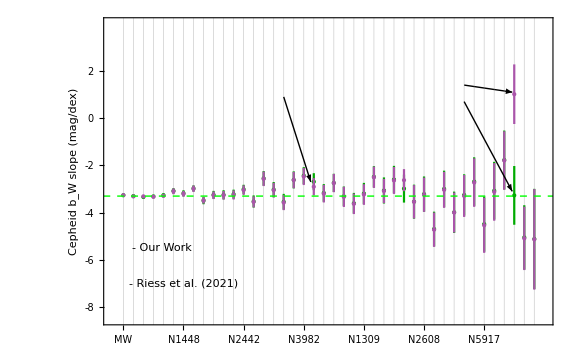
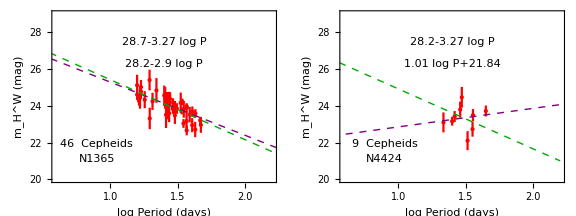

```mathematica
figb102bnocov=Show[plblack2,plsler2nocov,Graphics[{Arrowheads[0.015],Arrow[{{35,1.4},{39.8,1.1}}]}],Graphics[{Arrowheads[0.015],Arrow[{{35,0.7},{39.8,-3.1}}]}],Graphics[{Arrowheads[0.015],Arrow[{{17,0.9},{19.7,-2.7}}]}],Graphics[{Inset[Show[tabfigcsnocovinset[[7,2]],ImageSize->170],{12,1.2}],Dashed,Darker[Gray,0.1]}],Graphics[{Inset[Show[tabfigcsnocovinset[[22,2]],ImageSize->170],{30,1.2}],Dashed,Darker[Gray,0.1]}],Graphics[{Inset[" - Our Work ",{4.8,-5.5},BaseStyle->{Italic,Bold,Purple,FontFamily->"Times",16}]}],Graphics[{Inset[" - Riess et al. (2021) ",{7,-7},BaseStyle->{Italic,Bold,Darker[Green],FontFamily->"Times",16}]}],FrameStyle->Directive[Black,Thick],FrameTicks->{{{-8,-6,-4,-2,0,2},None},{{{1,Rotate["MW",90 Degree]},{2,Rotate["LMC",90 Degree]},{3,Rotate["SMC",90 Degree]},{4,Rotate["N4258",90 Degree]},{5,Rotate["M31",90 Degree]},{6,Rotate["N5643",90 Degree]},{7,Rotate["N1448",90 Degree]},{8,Rotate["M101",90 Degree]},{9,Rotate["N3447",90 Degree]},{10,Rotate["N5584",90 Degree]},{11,Rotate["N1559",90 Degree]},{12,Rotate["N4536",90 Degree]},{13,Rotate["N2442",90 Degree]},{14,Rotate["N3370",90 Degree]},{15,Rotate["N3583",90 Degree]},{16,Rotate["N3254",90 Degree]},{17,Rotate["N3972",90 Degree]},{18,Rotate["N5468",90 Degree]},{19,Rotate["N3982",90 Degree]},{20,Rotate["N1365",90 Degree]},{21,Rotate["N2525",90 Degree]},{22,Rotate["N7250",90 Degree]},{23,Rotate["U9391",90 Degree]},{24,Rotate["N1015",90 Degree]},{25,Rotate["N1309",90 Degree]},{26,Rotate["N5861",90 Degree]},{27,Rotate["N4639",90 Degree]},{28,Rotate["N0691",90 Degree]},{29,Rotate["N4038",90 Degree]},{30,Rotate["N7541",90 Degree]},{31,Rotate["N2608",90 Degree]},{32,Rotate["N3147",90 Degree]},{33,Rotate["N7329",90 Degree]},{34,Rotate["M1337",90 Degree]},{35,Rotate["N3021",90 Degree]},{36,Rotate["N7678",90 Degree]},{37,Rotate["N5917",90 Degree]},{38,Rotate["N4680",90 Degree]},{39,Rotate["N0976",90 Degree]},{40,Rotate["N4424",90 Degree]},{41,Rotate["N5728",90 Degree]},{42,Rotate["N0105",90 Degree]}},None}},PlotRange->{{-0.1,43},{-8.5,4.}},FrameTicksStyle->Directive[Thick,Black,FontFamily->"Helvetica",12], Frame->True,ImageSize->Large]
```

```mathematica
Export[NotebookDirectory[]<>"figb102bnocov.pdf",figb102bnocov,ImageResolution->1000];
```

## Results - Table C1

```mathematica
slopeernocovname[galrank_,taballnocov_]:=Table[{galrank[[i,4]],galrank[[i,5]],Round[taballnocov[[i,4]],0.01],Round[taballnocov[[i,5]],0.01]},{i,1,39}]
slernocovname=Join[slopeernocovname[galrank,taballnocov],{MW,0,-3.26,0.05}];
MatrixForm[slernocovname]
```

({M101,6.71,-2.99,0.14}
{M1337,38.53,-4.,0.85}
{N0691,35.4,-2.64,0.57}
{N1015,35.6,-3.63,0.43}
{N0105,73.8,-5.13,2.13}
{N1309,29.4,-3.23,0.44}
{N1365,22.8,-2.9,0.37}
{N1448,16.3,-3.21,0.12}
{N1559,19.3,-3.27,0.18}
{N2442,20.1,-3.05,0.2}
{N2525,27.2,-3.2,0.37}
{N2608,35.4,-3.24,0.73}
{N3021,26.6,-3.3,0.89}
{N3147,42.5,-4.72,0.73}
{N3254,24.4,-3.05,0.31}
{N3370,24,-3.55,0.23}
{N3447,20.8,-3.48,0.13}
{N3583,34.4,-2.57,0.31}
{N3972,15.1,-3.58,0.32}
{N3982,19,-2.47,0.36}
{N4038,29.3,-2.63,0.47}
{N4424,16.4,1.01,1.26}
{N4536,31.9,-3.25,0.19}
{N4639,19.8,-3.08,0.51}
{N4680,42.1,-3.12,1.22}
{N5468,46.3,-2.62,0.35}
{N5584,28,-3.26,0.16}
{N5643,20.7,-3.1,0.12}
{N5728,44.9,-5.09,1.34}
{N5861,30.3,-2.5,0.45}
{N5917,31,-4.54,1.17}
{N7250,12.8,-2.75,0.39}
{N7329,46.8,-3.04,0.76}
{N7541,34.4,-3.54,0.71}
{N7678,46.6,-2.73,1.03}
{N0976,60.5,-1.79,1.24}
{U9391,29.4,-3.33,0.43}
{N4258,7.4,-3.33,0.06}
{M31,0.86,-3.29,0.07}
MW
0
-3.26
0.05)